```mathematica
a1[x_]:= 1-x^2;
phih[x_,h_]:=(Exp[h*x]-1)/(h*x);
Table[phih[a1[x],.001],{x,-2,2,.05}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

{0.998501,0.9986,0.998696,0.99879,0.998881,0.998969,0.999056,0.999139,0.99922,0.999299,0.999375,0.999449,0.99952,0.999589,0.999655,0.999719,0.99978,0.999839,0.999895,0.999949,Indeterminate,1.00005,1.0001,1.00014,1.00018,1.00022,1.00026,1.00029,1.00032,1.00035,1.00038,1.0004,1.00042,1.00044,1.00046,1.00047,1.00048,1.00049,1.0005,1.0005,1.0005,1.0005,1.0005,1.00049,1.00048,1.00047,1.00046,1.00044,1.00042,1.0004,1.00038,1.00035,1.00032,1.00029,1.00026,1.00022,1.00018,1.00014,1.0001,1.00005,Indeterminate,0.999949,0.999895,0.999839,0.99978,0.999719,0.999655,0.999589,0.99952,0.999449,0.999375,0.999299,0.99922,0.999139,0.999056,0.998969,0.998881,0.99879,0.998696,0.9986,0.998501}

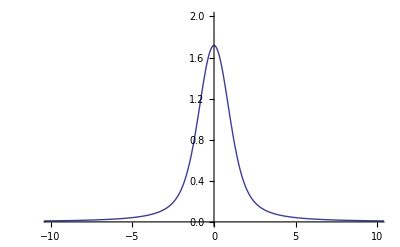

```mathematica
h:=1;
Plot[
{phih[a1[x],h]},
{x,-100,100},
PlotRange->{{-10,10},{0,2}},
PlotLegends->Automatic
]
```

```mathematica
f[x_]:=(Exp[h*a[x]]-1)/a[x];
```

```mathematica
f'[x]
```

-((-1+ⅇ^(h a[x])) a'[x])/a[x]^2+(ⅇ^(h a[x]) h a'[x])/a[x]